Hello! Welcome to our stellar evolution model. Below is an HR Diagram. Press shift enter on the cell to see it.

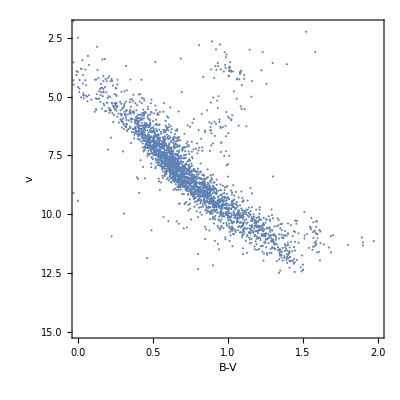

```mathematica
starData=SemanticImport["http://astrostatistics.psu.edu/datasets/HIP_star.dat"];
HRdiagram=ListPlot[starData[All,{"B-V","Vmag"}],ScalingFunctions->{Identity,"Reverse"},PlotStyle->Bold,Frame->True,AspectRatio->1,FrameLabel->{"B-V","v"},PlotRange->{{0,2},{15,2}}];
star=Plot[{},{x,-2,5},PlotRange->{{0,2},{15,2}},PlotStyle-> Red,Epilog->{AbsolutePointSize[5],Point[{1,7.5}]}];
Show[HRdiagram,star]
```

The HR diagram is a plot that astronomers use to measure where a star is in it’s lifetime. Stars start out on the main sequence, fusing hydrogen to helium, but eventually the store of hydrogen runs out and temperatures become high enough for the core to fuse past helium. When this happens a star’s luminosity, temperature, color, and even radius change, and the HR diagram is a great way to follow those changes. In this code, we found measured luminosities for different mass stars in some of the stages in it’s lifecycle and from there we calculated a lot of other properties. We plotted the star on small HR diagrams of temperature vs luminosity (in solar luminosities). 

Press shift enter on the next cell and input a mass to star!

```mathematica
userMass=Input["Enter a stellar mass between 1 and ?? (in solar masses). This will determine the evolution of your model star."];
If[userMass < 1,Print["Not enough mass for our model."],Print["You've made a star! Press shift enter on Main Sequence Cell."]]
```

You've made a star! Press shift enter on Main Sequence Cell.

Main Sequence, where our sun is right now. This is where the star spends the majority of it’s life, and the smaller the star, the longer the time. It’s where the star is fusing hydrogen to helium in it’s core.

Peak wavelength of light at 37.3625 nanometers. Lifespan of 821895. years!

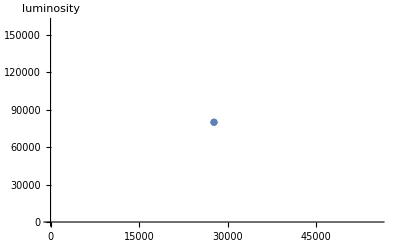

```mathematica
diagramPoint[mass_]:=Module[{peakλ,temp,radius,luminosity,lifespan},
If [mass >1 && mass≤1.5,luminosity=5];
If[mass>1.5&&mass≤3,luminosity=60];
If[mass>3&&mass≤5,luminosity=600];
If [mass>5&&mass≤10,luminosity=10000];
If[mass>10&&mass≤15,luminosity=17000];
If[mass>17&&mass≤25,luminosity=80000];
If [mass>25&&mass≤ 60,luminosity=790000];
radius=mass^(0.8);
temp=((luminosity*382.8*10^24)/(4 Pi (radius*6.95*10^8)^2 (5.67*10^-8)))^(1/4);
Return[{temp,luminosity}]
]
color[mass_,{luminosity_,temp_}]:=Module[{peakλ},
peakλ=(.002989)/temp;
peakλ=peakλ/(10^-9);
Return[peakλ];
]
lifespan=(10(userMass)^(-3))*10^9//N;
wavelength=color[userMass,diagramPoint[userMass]];
Print["Peak wavelength of light at ",wavelength," nanometers. Lifespan of ", lifespan," years!"]
star=ListPlot[{diagramPoint[userMass]},PlotRange-> All,AxesLabel->luminosity]
```

Red Giant stage, the star has stopped fusing hydrogen to helium in it’s core. Luminosity goes up, radius goes up, and temperature on the surface goes down.

Peak wavelength of light at 37.3625 nanometers.

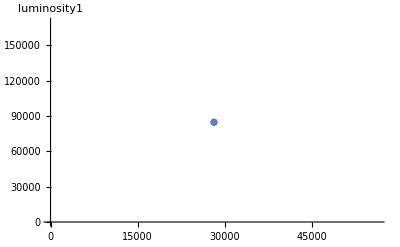

```mathematica
diagramPointGiant[mass_]:=Module[{temp1,radius1,luminosity1},
If[mass≤1,luminosity1=29];
If [mass >1 && mass≤5,luminosity1=170];
If [mass>5&&mass≤10,luminosity1=20800];
If[mass>10&&mass≤15,luminosity1=17000];
If[mass>15,luminosity1=84700];
radius1=mass^(0.8);
temp1=((luminosity1*382.8*10^24)/(4 Pi (radius1*6.95*10^8)^2 (5.67*10^-8)))^(1/4);
Return[{temp1,luminosity1}]
]
color1[mass_,{luminosity_,temp_}]:=Module[{peakλ1},
peakλ1=(.002989)/temp;
peakλ1=peakλ1/(10^-9);
Return[peakλ1];
]
giantwavelength=color1[userMass,diagramPointGiant[userMass]];
Print["Peak wavelength of light at ",wavelength," nanometers."]
giantstar=ListPlot[{diagramPointGiant[userMass]},PlotRange-> All,AxesLabel->luminosity1]
```

Asymptotic Giant Branch, or super giant stage, stops fusing in the core, but continues to fuse hydrogen and helium in outer shells.

Peak wavelength of light at 37.3625 nanometers.

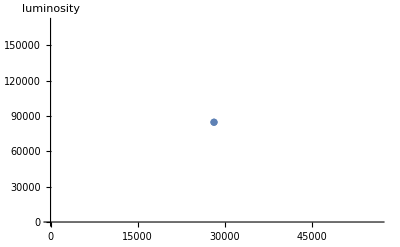

```mathematica
diagramPointSuperGiant[mass_]:=Module[{temp,radius,luminosity},
If [mass≤3,luminosity=10000];
If [mass>3&&mass≤5,luminosity=20000];
If[mass>5&&mass≤10,luminosity=29100];
If[mass>10 &&mass≤ 15,luminosity=40000];
If[mass>15&&mass≤ 20,luminosity=79100];
If[mass>20&&mass≤ 25,luminosity=429000];
If [mass>25,luminosity=1140000];
radius=mass^(0.8);
temp=((luminosity*382.8*10^24)/(4 Pi (radius*6.95*10^8)^2 (5.67*10^-8)))^(1/4);
Return[{temp,luminosity}]
]
color2[mass_,{luminosity_,temp_}]:=Module[{peakλ},
peakλ=(.002989)/temp;
peakλ=peakλ/(10^-9);
Return[peakλ];
]
supergiantwavelength=color2[userMass,diagramPointSuperGiant[userMass]];
Print["Peak wavelength of light at ",wavelength," nanometers."]
supergiantStar=ListPlot[{diagramPointGiant[userMass]},PlotRange-> All,AxesLabel->luminosity]
```

### Final Stage! All determined by mass.

```mathematica
If [userMass<8, Print["Your star was too small to ever become a neutron star or black hole, and instead became a beautiful planetary nebula!"]]
If [userMass>8 && userMass<25, Print["Your star was big enough that it became a neutron star! See the neutron star section below."]]
If [userMass>25, Print["Your star was so big that it became a BLACK HOLE, see black hole section below."]]
```

Your star was big enough that it became a neutron star! See the neutron star section below.

Neutron Star:

Radius of the neutron star:

```mathematica
Neutronstar[m_]=(18π)^(2/3)/10*(1.0545716*10^-34)/((6.67*10^-11)(m*1.9891*10^30)^(1/3))*1/(1.673532*10^-27);
Neutronstar[userMass]
```

3.89167×10^-8

Fun Facts:
The pressure inside of a Neutron star is so great that if you were a supervillain and could recreate that pressure, you could fit the whole population of the earth into a 1 cm cube. 
If you filled a shot glass with matter from a neutron star, that shot glass would weigh more than Mount Everest!

Black Hole:

Schwarzschild Radius (event horizon of the black hole):

```mathematica
blackhole[m_]=3(m);
blackhole[userMass]
Import["C:\\Users\\13607\\Downloads\\blackhole.png"]
```

3 usermass

-Graphics-

Fun Facts:
If you were to fall into a black hole, at just the right angle, you would see the death of the universe. This is because space would begin moving ever forward and time becomes the space we can move around in.
The gravity around a black hole is so great that is can bend light, this produces gravitational lensing around the event horizon of a black hole.